### Full Generality

```mathematica
γ = 1767732205903/4055673282236;
α = ({{1471266399579/7840856788654}, {-4482444167858/7529755066697}, {11266239266428/11593286722821}, {γ}});
c0=({{0}, {γ}, {3/5}, {1}});
c1=({{c11}, {c12}, {c13}, {c14}});
β1=({{β11}, {β12}, {β13}, {β14}});
β2=({{β21}, {β22}, {β23}, {β24}});
A0=({{0, 0, 0, 0}, {γ, γ, 0, 0}, {2746238789719/10658868560708, -640167445237/6845629431997, γ, 0}, {1471266399579/7840856788654, -4482444167858/7529755066697, 11266239266428/11593286722821, γ}}); (* A0=({{A011, A012, A013}, {A021, A022, A023}, {A031, A032, A033}}); *)
B0=({{0, 0, 0, 0}, {B021, 0, 0, 0}, {B031, B032, 0, 0}, {B041, B042, B043, 0}}); (* Subscript[B, 0]=({{B011, B012, B013}, {B021, B022, B023}, {B031, B032, B033}}); *)
H0=({{H01}, {H02}, {H03}, {H04}});
VU=({{U}, {U}, {U}, {U}});
e = ({{1}, {1}, {1}, {1}});
```

```mathematica
K1=IdentityMatrix[4] - μ h A0 ;
MatrixForm[K1 ]
```

(1 | 0 | 0 | 0
-(1767732205903 h μ)/4055673282236 | 1-(1767732205903 h μ)/4055673282236 | 0 | 0
-(2746238789719 h μ)/10658868560708 | (640167445237 h μ)/6845629431997 | 1-(1767732205903 h μ)/4055673282236 | 0
-(1471266399579 h μ)/7840856788654 | (4482444167858 h μ)/7529755066697 | -(11266239266428 h μ)/11593286722821 | 1-(1767732205903 h μ)/4055673282236)

```mathematica
K2 = VU + B0 . e  σ (σ I10)/h;
MatrixForm[K2]
```

(U
U+(B021 I10 σ^2)/h
U+((B031+B032) I10 σ^2)/h
U+((B041+B042+B043) I10 σ^2)/h)

```mathematica
H0= Inverse[K1].K2;
MatrixForm[H0]
```

(U
(U ((1767732205903 h μ)/4055673282236-(3124877151786686388045409 h^2 μ^2)/8224242886121464656579848+(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+((1-(1767732205903 h μ)/4055673282236)^2 (U+(B021 I10 σ^2)/h))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)
(U ((2746238789719 h μ)/10658868560708-(39263919217172690376234265775395010123 h^2 μ^2)/147964475510499162571292782416147033368+(80069332679609511347573991777528511637117244090351 h^3 μ^3)/1200191140095988760688488720422864050528741547301696))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+((-(640167445237 h μ)/6845629431997+(1131644610116089960634011 h^2 μ^2)/27763636387438637350105292) (U+(B021 I10 σ^2)/h))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+((1-(1767732205903 h μ)/4055673282236)^2 (U+((B031+B032) I10 σ^2)/h))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)
(U ((1471266399579 h μ)/7840856788654-(638608491010111964739057178390715420974136135184234902205933607 h^2 μ^2)/3698580106766471732936297308411592913459800398116270761990598228+(27829664413927281700477016041861656157393257425343106330929501 h^3 μ^3)/68457355489385529928894215620835335131094652557289360535699376544826011565810753245748384))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+((-(4482444167858 h μ)/7529755066697+(204302970945827751107628670993515621207876835684063 h^2 μ^2)/1211807897549370568026773283866266949575570488309102) (U+(B021 I10 σ^2)/h))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+(((11266239266428 h μ)/11593286722821-(4978923497668441242831121 h^2 μ^2)/11754645803761621258776939) (U+((B031+B032) I10 σ^2)/h))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+((1-(1767732205903 h μ)/4055673282236)^2 (U+((B041+B042+B043) I10 σ^2)/h))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256))

```mathematica
U2= U+ μ h αᵀ.H0 + σ I1 Transpose[e].β1+ σ I10/h Transpose[e].β2;
U2 =U2[[1]][[1]];
U2
```

U+I1 (β11+β12+β13+β14) σ+(I10 (β21+β22+β23+β24) σ)/h+h μ ((1471266399579 U)/7840856788654-(4482444167858 ((U ((1767732205903 h μ)/4055673282236-(3124877151786686388045409 h^2 μ^2)/8224242886121464656579848+(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+((1-(1767732205903 h μ)/4055673282236)^2 (U+(B021 I10 σ^2)/h))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)))/7529755066697+1/11593286722821 11266239266428 ((U ((2746238789719 h μ)/10658868560708-(39263919217172690376234265775395010123 h^2 μ^2)/147964475510499162571292782416147033368+(80069332679609511347573991777528511637117244090351 h^3 μ^3)/1200191140095988760688488720422864050528741547301696))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+((-(640167445237 h μ)/6845629431997+(1131644610116089960634011 h^2 μ^2)/27763636387438637350105292) (U+(B021 I10 σ^2)/h))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+((1-(1767732205903 h μ)/4055673282236)^2 (U+((B031+B032) I10 σ^2)/h))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256))+1/4055673282236 1767732205903 ((U ((1471266399579 h μ)/7840856788654-(638608491010111964739057178390715420974136135184234902205933607 h^2 μ^2)/3698580106766471732936297308411592913459800398116270761990598228+(27829664413927281700477016041861656157393257425343106330929501 h^3 μ^3)/68457355489385529928894215620835335131094652557289360535699376544826011565810753245748384))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+((-(4482444167858 h μ)/7529755066697+(204302970945827751107628670993515621207876835684063 h^2 μ^2)/1211807897549370568026773283866266949575570488309102) (U+(B021 I10 σ^2)/h))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+(((11266239266428 h μ)/11593286722821-(4978923497668441242831121 h^2 μ^2)/11754645803761621258776939) (U+((B031+B032) I10 σ^2)/h))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+((1-(1767732205903 h μ)/4055673282236)^2 (U+((B041+B042+B043) I10 σ^2)/h))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)))

```mathematica
I10=1/2 h(W+Z/(√3)); 
I1= W;
```

```mathematica
U2Full = U2
```

U+W (β11+β12+β13+β14) σ+1/2 (W+Z/(√3)) (β21+β22+β23+β24) σ+h μ ((1471266399579 U)/7840856788654-(4482444167858 ((U ((1767732205903 h μ)/4055673282236-(3124877151786686388045409 h^2 μ^2)/8224242886121464656579848+(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+((1-(1767732205903 h μ)/4055673282236)^2 (U+1/2 B021 (W+Z/(√3)) σ^2))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)))/7529755066697+1/11593286722821 11266239266428 ((U ((2746238789719 h μ)/10658868560708-(39263919217172690376234265775395010123 h^2 μ^2)/147964475510499162571292782416147033368+(80069332679609511347573991777528511637117244090351 h^3 μ^3)/1200191140095988760688488720422864050528741547301696))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+((-(640167445237 h μ)/6845629431997+(1131644610116089960634011 h^2 μ^2)/27763636387438637350105292) (U+1/2 B021 (W+Z/(√3)) σ^2))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+((1-(1767732205903 h μ)/4055673282236)^2 (U+1/2 (B031+B032) (W+Z/(√3)) σ^2))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256))+1/4055673282236 1767732205903 ((U ((1471266399579 h μ)/7840856788654-(638608491010111964739057178390715420974136135184234902205933607 h^2 μ^2)/3698580106766471732936297308411592913459800398116270761990598228+(27829664413927281700477016041861656157393257425343106330929501 h^3 μ^3)/68457355489385529928894215620835335131094652557289360535699376544826011565810753245748384))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+((-(4482444167858 h μ)/7529755066697+(204302970945827751107628670993515621207876835684063 h^2 μ^2)/1211807897549370568026773283866266949575570488309102) (U+1/2 B021 (W+Z/(√3)) σ^2))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+(((11266239266428 h μ)/11593286722821-(4978923497668441242831121 h^2 μ^2)/11754645803761621258776939) (U+1/2 (B031+B032) (W+Z/(√3)) σ^2))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+((1-(1767732205903 h μ)/4055673282236)^2 (U+1/2 (B041+B042+B043) (W+Z/(√3)) σ^2))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)))

```mathematica
U2Plugged = U2Full /.  {W -> 0,Z->0}
G = Coefficient[U2Plugged,U]
```

U+h μ ((1471266399579 U)/7840856788654+1/4055673282236 1767732205903 ((U (1-(1767732205903 h μ)/4055673282236)^2)/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+(U ((11266239266428 h μ)/11593286722821-(4978923497668441242831121 h^2 μ^2)/11754645803761621258776939))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+(U (-(4482444167858 h μ)/7529755066697+(204302970945827751107628670993515621207876835684063 h^2 μ^2)/1211807897549370568026773283866266949575570488309102))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+(U ((1471266399579 h μ)/7840856788654-(638608491010111964739057178390715420974136135184234902205933607 h^2 μ^2)/3698580106766471732936297308411592913459800398116270761990598228+(27829664413927281700477016041861656157393257425343106330929501 h^3 μ^3)/68457355489385529928894215620835335131094652557289360535699376544826011565810753245748384))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256))+1/11593286722821 11266239266428 ((U (1-(1767732205903 h μ)/4055673282236)^2)/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+(U (-(640167445237 h μ)/6845629431997+(1131644610116089960634011 h^2 μ^2)/27763636387438637350105292))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+(U ((2746238789719 h μ)/10658868560708-(39263919217172690376234265775395010123 h^2 μ^2)/147964475510499162571292782416147033368+(80069332679609511347573991777528511637117244090351 h^3 μ^3)/1200191140095988760688488720422864050528741547301696))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256))-(4482444167858 ((U (1-(1767732205903 h μ)/4055673282236)^2)/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)+(U ((1767732205903 h μ)/4055673282236-(3124877151786686388045409 h^2 μ^2)/8224242886121464656579848+(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256))/(1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256)))/7529755066697)

1+(1471266399579 h μ)/7840856788654+(287606284307616119269439395812053782939 h μ)/(354038415192410790619483213666362001932 (1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256))-(958434566372953418398985695336823336269590195300988728263749477453581558803 h^2 μ^2)/(1704670874492377712906933772898701682333029593648887685302346644152998742126 (1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256))-(3350866867971514617255290896933310993136969972246126212837979000600353762792866142579237599153336297 h^3 μ^3)/(138820333815416432112761307580493973049606844440304885935510728861666691655330297668303919424736453312 (1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256))+(8127196114498913430519281734369443912334834233333 h^4 μ^4)/(523061080853643875868745455264085362912575383735424 (1-(5303196617709 h μ)/4055673282236+(9374631455360059164136227 h^2 μ^2)/16448485772242929313159696-(5523945980703762886446374300101849327 h^3 μ^3)/66709684279724628271045721384347960256))

```mathematica
stableeq = FullSimplify[G/.  {μ -> z/h}]
```

-((2027836641118 (205372066468156589786682646862506005393283957671868081607098129634478034697432259737245152+z (-63172358211281746707151262345751745284607570169718188421714692711306385685801612264524032+z (-48808867189842884167640045981405766425900613210232968394498532488791459801764750086274170+83488993241781845101431048125584968472179772276029318992788503 z))))/(6242886710420635959355167587673092345451645772368478640901182031 (-4055673282236+1767732205903 z)^3))

```mathematica
GG[z_]:=-((2027836641118 (205372066468156589786682646862506005393283957671868081607098129634478034697432259737245152+z (-63172358211281746707151262345751745284607570169718188421714692711306385685801612264524032+z (-48808867189842884167640045981405766425900613210232968394498532488791459801764750086274170+83488993241781845101431048125584968472179772276029318992788503 z))))/(6242886710420635959355167587673092345451645772368478640901182031 (-4055673282236+1767732205903 z)^3))
```

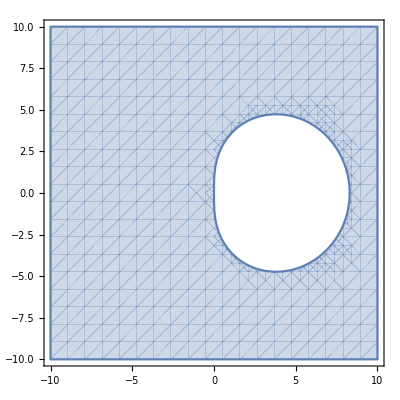

```mathematica
RegionPlot[Abs[GG[x+ⅈ y]]<1,{x,-10,10},{y,-10,10}]
```

```mathematica
cond1 = First[First[Transpose[α].e]] == 1;
cond2 = First[First[Transpose[β1].e]] == 1;
cond3 = First[First[Transpose[β2].e]] == 0;
cond4 = First[First[Transpose[α].B0.e]] == 1;
cond5 = First[First[Transpose[α].A0.e]] == 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] == 3/2;
cond7 = First[First[Transpose[β1].c1]] == 1;
cond8 = First[First[Transpose[β2].c1]] == -1;
```

```mathematica
conds = {cond2,cond3,cond4,cond6,cond7,cond8}
vars = {β11,β12,β13,β14,β21,β22,β23,β24,B021,B031,B032,B041,B042,B043,c11,c12,c13,c14};
```

{β11+β12+β13+β14==1,β21+β22+β23+β24==0,-(4482444167858 B021)/7529755066697+(11266239266428 B031)/11593286722821+(11266239266428 B032)/11593286722821+(1767732205903 B041)/4055673282236+(1767732205903 B042)/4055673282236+(1767732205903 B043)/4055673282236==1,-(4482444167858 B021^2)/7529755066697+(11266239266428 (B031+B032)^2)/11593286722821+(1767732205903 (B041+B042+B043)^2)/4055673282236==3/2,c11 β11+c12 β12+c13 β13+c14 β14==1,c11 β21+c12 β22+c13 β23+c14 β24==-1}

```mathematica
FindInstance[conds ,vars,Reals]
```

{{β11→0,β12→0,β13→0,β14→1,β21→1,β22→0,β23→0,β24→-1,B021→(-354038415192410790619483213666362001932+(87294609440832483406992237 (-53983406399371387722712393713535786276-26826820 √6853072660943221216270384658311461343029149665543510113394397))/4868738516734691891458097)/210758174113231167877981435258781706648,B031→0,B032→0,B041→0,B042→0,B043→(-53983406399371387722712393713535786276-26826820 √6853072660943221216270384658311461343029149665543510113394397)/8606625878152317177894269252900546591,c11→0,c12→0,c13→0,c14→1}}